# Crossword Puzzle Solver Martins Samuel, 2015

```mathematica
(* number of rows and columns *)
{i,j}={5,5};
```

```mathematica
(* generate random letters & assign numbers to them *)
vshape=With[{alphlist=RandomChoice[CharacterRange["A","Z"],i j]},
Catenate[Table[{v->Graphics[{Black,Text[Style[alphlist⟦v⟧,White,10]]}]},{v,1,i j}]]];

Block[
{
(* create vertices out of numbers to form grid *)
rows=Complement[Table[jj<->jj+i,{jj,1,i*(j-1)}],Table[r j<->(r j)+1,{r,1,j}]],
cols=Complement[Table[ii<->ii+1,{ii,1,i j}],Table[c i<->c i+1,{c,1,j}]],
maindiag=Delete[Table[m<->m+i-1,{m,1,(i j)-i,1}],({#}&/@Range[1,i*(j-1),i])],
antidiag=Delete[Table[a<->a+i+1,{a,1,(i j)-i,1}],({#}&/@Range[i,i*(j-1),i])],

verts,vertlabels
},

(* style change b/w vshape & vertlabels *)
verts=vshape⟦All,2,1,2⟧;
vertlabels=(Keys[vshape]⟦#⟧->Style[ToString@verts⟦#,1⟧,White,10])&/@Range[1,i j];

graph1=Graph[Join[cols,rows,antidiag,maindiag],GraphLayout->{"GridEmbedding","Dimension"->{i,j}},EdgeStyle-> Directive[White,Opacity[0],Thin],VertexShape->vertlabels,VertexStyle->Black,VertexSize->0.5,ImageSize->All];

(* linking each number to "it's" letter *)
arr=(Keys[vshape]⟦#⟧->ToLowerCase@ToString@verts⟦#,1⟧)&/@Range[i j];
revarr=(ToLowerCase@ToString@verts⟦#,1⟧->Keys[vshape]⟦#⟧)&/@Range[i j];

]
```

```mathematica
(* scan graph to generate permutations *)
(* VERTlinescan = Table[(Table[FoldList[#1+#2&,x,Table[1,{n}]],{n,1,i-x}]),{x,1,i-1,1}]; *)
allVERTscan=(Table[(Table[FoldList[#1+#2&,x+#,Table[1,{n}]],{n,1,i-x}]),{x,1,i-1,1}])&/@Range[0,(i*j)-i,i];

(* HORIZlinescan = Table[(Table[FoldList[#1+#2&,1+(x*i),Table[i,{n}]],{n,1,j-x-1}]),{x,0,j-2}]; *)
allHORIZscan=(Table[(Table[FoldList[#1+#2&,#+(x*i),Table[i,{n}]],{n,1,j-x-1}]),{x,0,j-2}])&/@Range[1,i];


(*
 MAINlinescan=Cases[Table[Reverse@Diagonal[Reverse@Partition[Range[i*j],i],d],{d,Range[-i,i-2,1]}],{__,__}]; 
allMAINscan=Table[(FoldList[Append,{},MAINlinescan⟦x⟧])⟦4;;⟧,{x,1,Length@MAINlinescan}]; (this is incomplete: doesn't find combinations for inner part of the grid.)
*)
MAINlinescan=Cases[Table[Reverse@Diagonal[Reverse@Partition[Range[i j],i],d],{d,Range[-i,i-2,1]}],{__,__}];
allMAINscan=Block[{nums},
nums=Flatten[Table[(FoldList[Append,{},#⟦x⟧])⟦4;;⟧,{x,1,Length@#}],1]&[MAINlinescan];
Flatten[Table[Table[nums⟦len,n;;⟧,{n,1,Length@nums⟦len⟧-1}],{len,1,Length@nums,1}],1]
];

(*
 ANTlinescan=Cases[Table[Reverse@Diagonal[Partition[Range[i*j],i],d],{d,Range[-i,i-2,1]}],{__,__}]; 
allANTscan=Table[(FoldList[Append,{},ANTlinescan⟦x⟧])⟦2;;⟧,{x,1,Length@ANTlinescan}];
(this is incomplete: doesn't find combinations for inner part of the grid.)
*)
 ANTlinescan=Cases[Table[Reverse@Diagonal[Partition[Range[i*j],i],d],{d,Range[-i,i-2,1]}],{__,__}]; 
allANTscan=Block[{nums},
nums=Flatten[Table[(FoldList[Append,{},#⟦x⟧])⟦4;;⟧,{x,1,Length@#}],1]&[ANTlinescan];
Flatten[Table[Table[nums⟦len,n;;⟧,{n,1,Length@nums⟦len⟧-1}],{len,1,Length@nums,1}],1]
];

(* horizontal & vertical scanning & puzzle solving *)
(*horizontal*)
Block[
{numlistHORIZ=Cases[Flatten[{#,Map[Reverse,#,3],2},3],{_,_,_,___}]&[allHORIZscan],
stringlistHORIZ,numlinkHORIZ,wordlinkHORIZ},

stringlistHORIZ=Map[StringJoin,numlistHORIZ/.arr];
numlinkHORIZ=Thread[Range@Length@#->#]&[stringlistHORIZ];
wordlinkHORIZ=DeleteCases[ParallelTable[If[MemberQ[DictionaryLookup[],stringlistHORIZ⟦wl⟧]==True,#⟦wl⟧],{wl,Keys@#}],Null]&[numlinkHORIZ];

HORIZwords=DeleteCases[ParallelTable[If[(MemberQ[DictionaryLookup[],hw]&&StringLength[hw]>2)==True,hw],{hw,stringlistHORIZ}],Null];
linksHORIZ=ParallelTable[numlistHORIZ⟦n⟧,{n,Keys@wordlinkHORIZ}];
intsHORIZ=Block[{l},
Table[(l=Length@#⟦n⟧;Table[#⟦n,l⟧<->#⟦n,l+1⟧,{l,Range@(l-1)}]),
{n,Range@Length@#}]&[linksHORIZ]
]
];

(* vertical *)
Block[
{numlistVERT=Cases[Flatten[{#,Map[Reverse,#,3],2},3],{_,_,_,___}]&[allVERTscan],
stringlistVERT,numlinkVERT,wordlinkVERT},

stringlistVERT=Map[StringJoin,numlistVERT/.arr];
numlinkVERT=Thread[Range@Length@#->#]&[stringlistVERT];
wordlinkVERT=DeleteCases[ParallelTable[If[MemberQ[DictionaryLookup[],stringlistVERT⟦wlv⟧]==True,#⟦wlv⟧],{wlv,Keys@#}],Null]&[numlinkVERT];

VERTwords=DeleteCases[ParallelTable[If[(MemberQ[DictionaryLookup[],vw]&&StringLength[vw]>2)==True,vw],{vw,stringlistVERT}],Null];
linksVERT=ParallelTable[numlistVERT⟦n⟧,{n,Keys@wordlinkVERT}];
intsVERT=Block[{l},
Table[(l=Length@#⟦n⟧;
Table[#⟦n,l⟧<->#⟦n,l+1⟧,{l,Range@(l-1)}]),
{n,Range@Length@#}]&[linksVERT]
]
];

(* main diagonal & anti-diagonal scanning & puzzle solving *)
(* main diagonal *)

Block[
{numlistMAIN=Cases[Flatten[{#,Reverse/@#,2},1],{_,_,_,___}]&[allMAINscan],
stringlistMAIN,numlinkMAIN,wordlinkMAIN},

stringlistMAIN=Map[StringJoin,numlistMAIN/.arr];
numlinkMAIN=Thread[Range@Length@#->#]&[stringlistMAIN];
wordlinkMAIN=DeleteCases[ParallelTable[If[MemberQ[DictionaryLookup[],stringlistMAIN⟦wlm⟧]==True,#⟦wlm⟧],{wlm,Keys@#}],Null]&[numlinkMAIN];

MAINwords=DeleteCases[ParallelTable[If[(MemberQ[DictionaryLookup[],mw]&&StringLength[mw]>2)==True,mw],{mw,stringlistMAIN}],Null];
linksMAIN=ParallelTable[numlistMAIN⟦n⟧,{n,Keys@wordlinkMAIN}];
intsMAIN=Block[{l},
Table[(l=Length@#⟦n⟧;
Table[#⟦n,l⟧<->#⟦n,l+1⟧,{l,Range@(l-1)}]),{n,Range@Length@#}]&[linksMAIN]
]
];

(* anti-diagonal *)
Block[
{numlistANT=Cases[Flatten[{#,Reverse/@#,2},1],{_,_,_,___}]&[allANTscan],
stringlistANT,numlinkANT,wordlinkANT},

stringlistANT=Map[StringJoin,numlistANT/.arr];
numlinkANT=Thread[Range@Length@#->#]&[stringlistANT];
wordlinkANT=DeleteCases[ParallelTable[If[MemberQ[DictionaryLookup[],stringlistANT⟦wla⟧]==True,#⟦wla⟧],{wla,Keys@#}],Null]&[numlinkANT];

ANTwords=DeleteCases[ParallelTable[If[(MemberQ[DictionaryLookup[],aw]&&StringLength[aw]>2)==True,aw],{aw,stringlistANT}],Null];
linksANT=ParallelTable[numlistANT[[n]],{n,Keys@wordlinkANT}];
intsANT=Block[{l},
Table[(l=Length@#⟦n⟧;
Table[#⟦n,l⟧<->#⟦n,l+1⟧,{l,Range@(l-1)}]),{n,Range@Length@#}]&[linksANT]
]
];
```

```mathematica
(* colour / frequency chart *)
chartvis=Block[{chart},
chart[{reccol_,len_}]:=
Multicolumn[Table[Graphics[{reccol,Rectangle[]},AspectRatio->1/10,ImageSize->15],{Length@len}],{Automatic,5}];

Rotate[Column[
chart/@Reverse@SortBy[{
{ColorData["HTML","ColorList"]⟦42⟧,linksANT},
{Darker@Green,linksVERT},
{Red,linksMAIN},
{Orange,linksHORIZ}
},Last]
],90Degree]
];
```

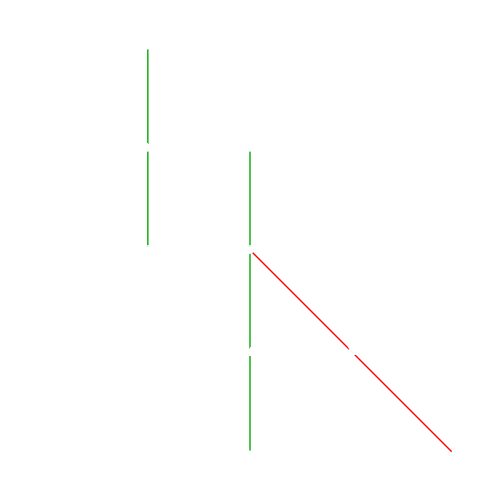
-Graphics- | across


 | down


VIE
VIEW
RIB | main
diagonal

AWE | antidiagonal



 | -Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- |  |  |  | 
 |  |  |  | 
 |  |  |  |

```mathematica
Block[
{hi,wordstyle,grid,puzzle1,puzzle2},

hi=HighlightGraph[
graph1,
Join[
Thread[Style[intsHORIZ,Orange,Opacity[1],Thickness[0.002]]],
Thread[Style[intsVERT,Darker@Green,Opacity[1],Thickness[0.002]]],
Thread[Style[intsMAIN,Red,Opacity[1],Thickness[0.002]]],
Thread[Style[intsANT,ColorData["HTML","ColorList"]⟦42⟧,Opacity[1],Thickness[0.002]]]
],ImageSize->500];

wordstyle[dir__String,words_List,colour_]:=Style[
Column[{
Style[dir,Italic,Gray,15],
Multicolumn[ToUpperCase@words,If[Length@words>22,2,1]]},Alignment->Center],
colour,10,FontFamily->"Avenir Next"];

grid=Grid[{{
wordstyle["across\n\n",Sort@HORIZwords,Orange],
wordstyle["down\n\n",Sort@VERTwords,Darker@Green],
wordstyle["main\ndiagonal\n",Sort@MAINwords,Red],
wordstyle["antidiagonal\n\n",Sort@ANTwords,ColorData["HTML","ColorList"]⟦42⟧]
}},Alignment->Top,Spacings->{2,0},ItemSize->Larger];

(* show results without background (text is white right now, so won't be clear without background) *)
puzzle1=GraphicsGrid[{{
hi,
grid
}},
ImageSize->800,Spacings->{Scaled[.1],0}];


puzzle2=Grid[{
{
Item[hi,Background->Lighter[Black,.1],ItemSize->All],
Item[grid,Background->Lighter[Black,.15]]
},
{
SpanFromAbove,Item[chartvis,Background->Lighter[Black,.125],ItemSize->{15,15}]
}
},Alignment->{Center,Center},Spacings->{Scaled[.25],0},Frame->All]

]
```

```mathematica
Quit[]
```